{Cos[t] (3+Sin[5 t]),Sin[t] (3+Sin[5 t])}

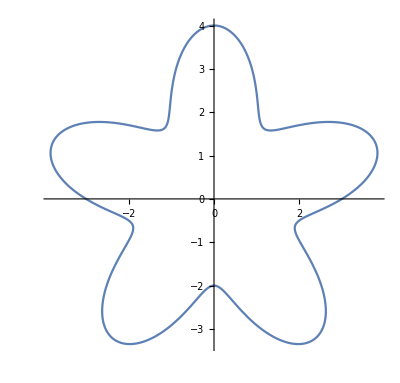

```mathematica
x[t_]=3 Cos[t];
y[t_]=3Sin[t];
c[t_]={x[t],y[t]};
ut[t_]=c'[t]/Sqrt[c'[t].c'[t]];
un[t_]=-ut'[t]/Sqrt[ut'[t].ut'[t]];
p[t_]=FullSimplify[c[t]+un[t]*Sin[5 t]]
ParametricPlot[p[t],{t,0,2Pi}]
```

```mathematica
{x[t_],y[t_],z[t_]} = {Sin[t],Sin[2 t+ Pi/5],Sin[3 t + Pi/7]};
curve=ParametricPlot3D[{x[t],y[t],z[t]},{t,0,2Pi}]
Export["curve.jpg",curve,ImageResolution->300]
```

-Graphics3D-

curve.jpg

```mathematica
{x[t_],y[t_],z[t_]} = {Sin[t],Sin[2 t+ Pi/5],Sin[3 t + Pi/7]};
unitTan[t_]={x'[t],y'[t],z'[t]}/(Sqrt[{x'[t],y'[t],z'[t]}.{x'[t],y'[t],z'[t]}]);
unitNormal[t_]=unitTan'[t]/Sqrt[unitTan'[t].unitTan'[t]];
biNormal[t_]=Cross[unitTan[t],unitNormal[t]];
thickness=.10;
tube=ParametricPlot3D[{x[t],y[t],z[t]}+thickness*(Cos[s]*unitNormal[t] + Sin[s]*biNormal[t]),{t,0,2Pi},{s,0,2Pi},Mesh->{40,10}]
Export["tube.jpg",tube,ImageResolution->300]
```

-Graphics3D-

tube.jpg

```mathematica
p[t_] = {t^2-2,1t^2-2,-t+1};
paraCurve=ParametricPlot3D[p[t],{t,-3,3},PlotRange->{{-3,3},{-3,3},{-2,3}}]
unitTan[t_]=Simplify[p'[t]/Sqrt[p'[t].p'[t]]]
unitNormal[t_]=Simplify[unitTan'[t]/Sqrt[unitTan'[t].unitTan'[t]]];
unitBinormal[t_]=FullSimplify[Cross[unitTan[t],unitNormal[t]]];
normalArrows=Graphics3D[{Red,Table[Arrow[Tube[{p[t],1*unitNormal[t]+p[t]}]],{t,-5,5,.6}]}];
binormalArrows=Graphics3D[{Blue,Table[Arrow[Tube[{p[t],1*unitBinormal[t]+p[t]}]],{t,-5,5,.6}]}];
paraArrows=Show[curve,normalArrows,binormalArrows]
Export["paraCurve.jpg",paraCurve,ImageResolution->300]
(*Export["paraArrows.jpg",paraArrows,ImageResolution->300]*)
```

-Graphics3D-

{(2 t)/(√(1+8 t^2)),(2 t)/(√(1+8 t^2)),-1/(√(1+8 t^2))}

Show::gcomb: Could not combine the graphics objects in curve, Graphics3DBox[List[RGBColor[1, 0, 0], List[Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]]]]], Graphics3DBox[List[RGBColor[0, 0, 1], List[Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]], Arrow3DBox[TubeBox[List[List[Skeleton[3]], List[Skeleton[3]]]]]]]].

Show[curve,-Graphics3D-,-Graphics3D-]

paraCurve.jpg

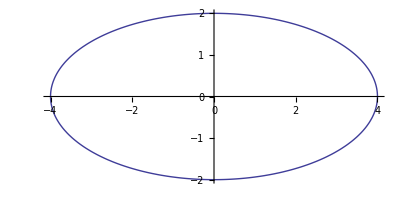

hole.jpg

```mathematica
hole=ParametricPlot[{4Cos[t],2Sin[t]},{t,0,2Pi}]
Export["hole.jpg",hole,ImageResolution->300]
```

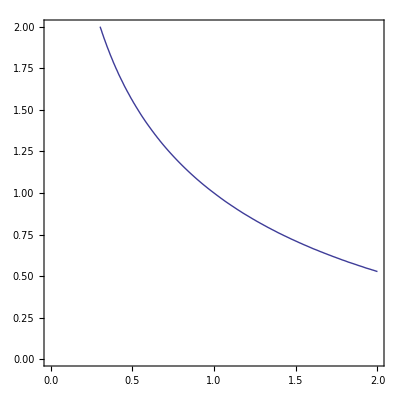

lc.jpg

```mathematica
lc=ContourPlot[x^2 y^3 E^(x+y)==7.38906,{x,0,2},{y,0,2}]
Export["lc.jpg",lc,ImageResolution->300]
```